```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/LaTeX-Files/中级化学实验报告/data/Fluorescence"];
Table[A[i]=Cases[Import[#[[i]],"Table"],{_Real,_Real}],{i,1,Length[#]}]&@FileNames["*.TXT"];
```

```mathematica
TableForm[Transpose[{Range[Length[#]],#}]&@FileNames["*.TXT"]]
```

1 | 0_5_2ND.TXT
2 | 0_5EM2ND.TXT
3 | 0_5EMIT'.TXT
4 | 0_5EMIT.TXT
5 | 0_5'.TXT
6 | 0_5.TXT
7 | 10MLACOH.TXT
8 | 20MLACOH.TXT
9 | 5MLACOH.TXT
10 | BACK'.TXT
11 | BACK.TXT
12 | PH_MIN'.TXT
13 | PH_MIN.TXT
14 | STANDARD.TXT
15 | UNKNOWN.TXT

```mathematica
A[14]
```

{}

```mathematica
Fit[{#1/25*10,#2}&@@@(Drop[#,1]&/@Cases[Import[#,"Table"],{_Integer,_Real,_Real}]&@"STANDARD.TXT"),{1,x},x]
```

14.1588+2734.31 x

```mathematica
Solve[14.158799999999832+2734.3137499999993 x==272.407,x]
```

{{x→0.0944472}}

```mathematica
LinearModelFit[{#1/25*10,#2}&@@@(Drop[#,1]&/@Cases[Import[#,"Table"],{_Integer,_Real,_Real}]&@"STANDARD.TXT"),{1,x},x]["RSquared"]
```

0.999613

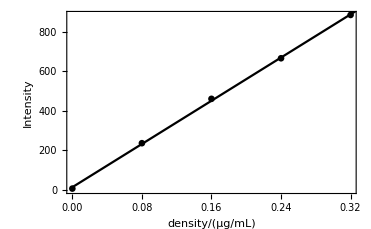

```mathematica
Show[
ListPlot[#,Axes->False,Frame->True,PlotStyle->Black,FrameLabel->{"density/(μg/mL)","Intensity"}],
Plot[14.158799999999832+2734.3137499999993 x,{x,0,1},PlotStyle->Black]
]&@({#1/25*10,#2}&@@@(Drop[#,1]&/@Cases[Import[#,"Table"],{_Integer,_Real,_Real}]&@"STANDARD.TXT"))
```

```mathematica
Export["Standardcurve.eps",%]
```

Standardcurve.eps

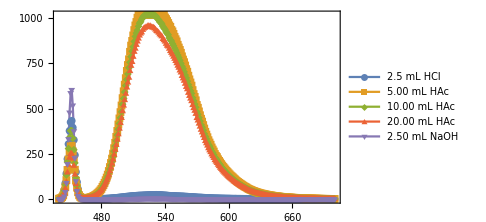

```mathematica
ListLinePlot[{A[13],A[9],A[7],A[8],({#1,50(#2/100)^1.7}&@@@A[13])},PlotRange->All,PlotMarkers->{Automatic,8},ImageSize->Medium,Frame->True,Axes->False,PlotLegends->{"2.5 mL HCl","5.00 mL HAc","10.00 mL HAc","20.00 mL HAc","2.50 mL NaOH"},ImageSize->Large]
```

```mathematica
Position[#,1]&/@(PeakDetect[#,0,2,200]&/@(#2&@@@Transpose/@{A[13],A[9],A[7],A[8],({#1,50(#2/100)^1.7}&@@@A[13])}))
```

{{{13}},{{13}},{{12},{83}},{{13},{85},{87}},{{13}}}

```mathematica
functionlist=Interpolation[#][x]&/@{A[13],A[9],A[7],A[8],({#1,50(#2/100)^1.7}&@@@A[13])};
```

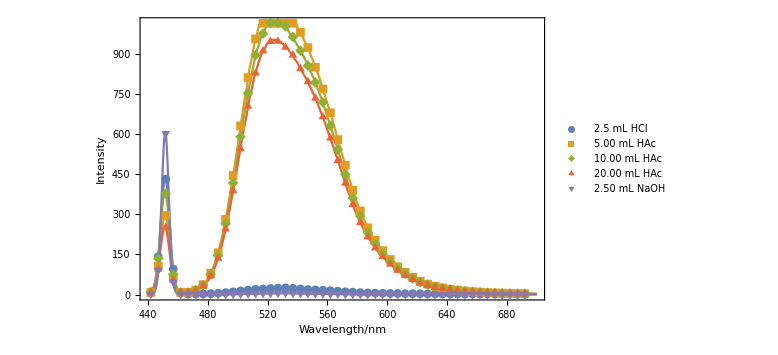

```mathematica
Show[Plot[functionlist,{x,440,700},PlotRange->All,ImageSize->Medium,Frame->True,Axes->False,ImageSize->Large,FrameLabel->{"Wavelength/nm","Intensity"}],ListPlot[Part[#,Table[5i+3,{i,0,50}]]&/@{A[13],A[9],A[7],A[8],({#1,50(#2/100)^1.7}&@@@A[13])},PlotMarkers->Automatic,PlotLegends->{"2.5 mL HCl","5.00 mL HAc","10.00 mL HAc","20.00 mL HAc","2.50 mL NaOH"},FrameTicks->True],ImageSize->Large]
```

```mathematica
Export["pH.eps",%]
```

pH.eps

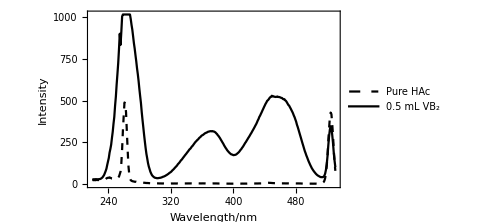

```mathematica
ListLinePlot[{A[11],A[6]},PlotRange->All,ImageSize->Medium,Frame->True,PlotStyle->{{Black,Dashed},{Black}},Axes->False,PlotLegends->{"Pure HAc","0.5 mL VB_2"},FrameLabel->{"Wavelength/nm","Intensity"}]
```

```mathematica
Export["expose.eps",%]
```

expose.eps

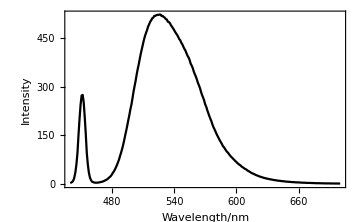

```mathematica
ListLinePlot[A[4],PlotRange->All,ImageSize->Medium,Frame->True,PlotStyle->Black,Axes->False,FrameLabel->{"Wavelength/nm","Intensity"}]
```

```mathematica
Export["emission.eps",%]
```

emission.eps

```mathematica
({#1/25*10,#2}&@@@(Drop[#,1]&/@Cases[Import[#,"Table"],{_Integer,_Real,_Real}]&@"STANDARD.TXT"))//Transpose//TableForm//TeXForm
```

\begin{array}{ccccc}
 0. & 0.08 & 0.16 & 0.24 & 0.32 \\
 7.154 & 236.915 & 461.473 & 666.732 & 885.971 \\
\end{array}

```mathematica
-Log10/@(ComplexH[{#/60.06,0},{1.8*10^(-5)}]&/@{1/5,10/25,20/25})
```

{3.6271,3.47191,3.31809}

```mathematica
-Log10@ComplexH[{0.6,0},{10000}]
```

0.221875

```mathematica
-Log10@ComplexH[{0,10/40/10},{0}]
```

12.3979

```mathematica
FindFit[Drop[A[4],84],a E^((x-μ)^2/(2 σ^2))(1-E^(k x))+b,{a,σ,μ,k,b},x]
```

Drop::drop: Cannot drop positions 1 through 84 in A[4].

FindFit::fitd: First argument Drop[A[4],84] in FindFit is not a list or a rectangular array.

FindFit[Drop[A[4],84],b+a ⅇ^((x-μ)^2/(2 σ^2)) (1-ⅇ^(k x)),{a,σ,μ,k,b},x]

```mathematica
Drop[A[4],84]
```

{{524.,521.506},{525.,521.359},{526.,522.496},{527.,522.154},{528.,517.867},{529.,518.268},{530.,514.76},{531.,513.079},{532.,508.722},{533.,507.168},{534.,500.293},{535.,499.224},{536.,495.835},{537.,489.656},{538.,484.948},{539.,479.998},{540.,474.977},{541.,469.252},{542.,464.138},{543.,459.471},{544.,453.627},{545.,446.725},{546.,443.147},{547.,435.361},{548.,430.658},{549.,423.093},{550.,416.429},{551.,411.197},{552.,402.821},{553.,395.363},{554.,390.293},{555.,382.309},{556.,371.174},{557.,365.144},{558.,357.615},{559.,347.074},{560.,338.575},{561.,331.374},{562.,322.162},{563.,311.74},{564.,304.197},{565.,295.519},{566.,284.246},{567.,274.28},{568.,266.709},{569.,257.575},{570.,245.764},{571.,238.457},{572.,227.775},{573.,218.688},{574.,209.528},{575.,201.332},{576.,193.621},{577.,183.56},{578.,175.382},{579.,168.841},{580.,161.659},{581.,154.175},{582.,147.856},{583.,141.713},{584.,135.154},{585.,129.838},{586.,124.108},{587.,117.701},{588.,113.928},{589.,109.168},{590.,103.951},{591.,99.762},{592.,96.715},{593.,92.215},{594.,87.976},{595.,84.321},{596.,81.402},{597.,77.9},{598.,74.636},{599.,71.168},{600.,68.56},{601.,65.215},{602.,62.175},{603.,59.926},{604.,57.72},{605.,54.532},{606.,52.338},{607.,50.386},{608.,47.718},{609.,46.331},{610.,44.091},{611.,41.602},{612.,39.882},{613.,37.974},{614.,35.741},{615.,33.68},{616.,32.852},{617.,31.119},{618.,29.594},{619.,27.907},{620.,26.799},{621.,25.519},{622.,24.069},{623.,23.228},{624.,22.033},{625.,21.163},{626.,20.007},{627.,19.107},{628.,18.465},{629.,17.338},{630.,17.06},{631.,16.015},{632.,15.418},{633.,14.942},{634.,14.12},{635.,13.688},{636.,13.028},{637.,12.355},{638.,12.21},{639.,11.354},{640.,11.175},{641.,10.622},{642.,10.34},{643.,9.806},{644.,9.318},{645.,9.138},{646.,8.864},{647.,8.282},{648.,8.055},{649.,7.689},{650.,7.524},{651.,7.28},{652.,7.125},{653.,6.515},{654.,6.476},{655.,6.306},{656.,6.044},{657.,5.769},{658.,5.559},{659.,5.503},{660.,5.517},{661.,5.251},{662.,5.074},{663.,4.642},{664.,4.604},{665.,4.555},{666.,4.413},{667.,4.252},{668.,3.956},{669.,3.955},{670.,3.945},{671.,3.932},{672.,3.69},{673.,3.522},{674.,3.588},{675.,3.321},{676.,3.232},{677.,2.99},{678.,2.977},{679.,3.192},{680.,2.904},{681.,2.891},{682.,2.852},{683.,2.696},{684.,2.625},{685.,2.564},{686.,2.408},{687.,2.478},{688.,2.421},{689.,2.508},{690.,2.329},{691.,2.276},{692.,2.192},{693.,2.273},{694.,2.211},{695.,2.073},{696.,2.133},{697.,2.128},{698.,2.025},{699.,2.018},{700.,2.023}}

```mathematica
-Log10/@(ComplexH[{#/60.06,0},{1.8*10^(-5)}]&/@{1/5,10/25,20/25})

-Log10@ComplexH[{0.6,0},{10000}]

-Log10@ComplexH[{0,10/40/10},{0}]
```

{3.6271,3.47191,3.31809}

0.221875

12.3979

```mathematica
25/0.4*0.0944
```

5.9

```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/LaTeX-Files/中级化学实验报告/data/Chromatography"];
```

```mathematica
FileNames[]
```

{std-01.txt,std-02.txt,std-03.txt,std-04.txt,std-05.txt,std-06.txt,std-07.txt,std-08.txt,std-09.txt,std-10.txt,std-11.txt,std-12.txt}

```mathematica
Table[A[i]=Cases[Import[#[[i]],"Table"],{_Real,_Integer}],{i,1,Length[#]}]&@FileNames["*.TXT"];
```

```mathematica
"Standardextension.eps"~Export~ListLinePlot[Select[#,#[[1]]>1&]&/@A/@Range[6],PlotRange->All,PlotStyle->Thickness[0.002],Frame->True,Axes->False,ImageSize->Medium,PlotLegends->{0.2,0.4,0.5,0.6,0.8,1.0}/5*1000]
```

Standardextension.eps

```mathematica
"Standardextensionsolvent.eps"~Export~ListLinePlot[Select[#,0<#[[1]]<1.16&]&/@A/@Range[6],PlotRange->All,PlotStyle->Thickness[0.002],Frame->True,Axes->False,PlotLegends->{0.2,0.4,0.5,0.6,0.8,1.0}/5*1000]
```

Standardextensionsolvent.eps

```mathematica
"ratio.eps"~Export~ListLinePlot[Select[#,#[[1]]>1&]&/@A/@{7,11,12},PlotRange->All,PlotStyle->Thickness[0.002],Frame->True,Axes->False,ImageSize->Medium,PlotLegends->ToString/@{"80:20","70:30","65:35"}]
```

ratio.eps

```mathematica
#2&@@@Select[#,1.4<#[[1]]<1.5&]&/@A/@Range[6]
```

{{3773,2162,1439,1155,1108,1213,1698,4164,14588},{13877,7410,4431,3128,2628,2531,2729,3814,9535},{15634,8374,5044,3592,3040,2928,3124,4151,9576},{17134,9364,5824,4309,3757,3681,4043,5924,15801},{19536,10956,7108,5497,4944,4932,5519,8511,24059},{37049,19543,11491,7937,6504,6080,6225,7296,12875}}

```mathematica
"Standardextensionmedium.eps"~Export~ListLinePlot[Select[#,1.4<#[[1]]<1.5&]&/@A/@Range[6],PlotStyle->Thickness[0.001],ImageSize->Large,Frame->True,Axes->False]
```

Standardextensionmedium.eps

```mathematica
standard={{{1.312,1257344,344731},{1.548,1097148,273118},{1.777,1015037,232326}},
{{1.321,2767414,756678},{1.558,2409631,602078},{1.789,2231886,513746}},
{{1.320,3228160,886589},{1.559,2809237,706920},{1.792,2607079,607608}},
{{1.317,4069330,1084438},{1.557,3541307,881417},{1.790,3287100,756536}},
{{1.315,5356016,1460194},{1.555,4683383,1168334},{1.790,4354363,10006866}},
{{1.323,6550644,1798912},{1.563,5763248,1416618},{1.798,5363409,1232525}}};
unknown={{{1.324,3319980,973649},{1.566,2887152,765530},{1.802,2676464,659082}},{{1.317,3602989,1028006},{1.559,3134953,832917},{1.796,2908242,707690}},
{{1.326,3778152,1093799},{1.569,3286537,874645},{1.806,3049488,743346}}};
fluid={{{1.324,3319980,973649},{1.566,2887152,765530},{1.802,2676464,659082}},
{{1.472,8408764,2074508},{2.076,7465018,1518307},{2.764,6997466,1190681}},
{{1.470,7600126,1888329},{2.079,6739076,1384434},{2.793,6316958,962652}}};
```

```mathematica
Plot[Normal/@(LinearModelFit[#,{1,x},x]&/@(Transpose[#][[2]]&/@standard//Transpose)),{x,0,
```

{364137.+1.0021×10^6 x,295610.+882395. x,264214.+822552. x}

```mathematica
Normal/@(LinearModelFit[#,{1,x},x]&/@Transpose[{{0.2,0.4,0.5,0.6,0.8,1.0}/5*1000,#}]&/@(Transpose[#][[2]]&/@standard//Transpose))
```

{{-1.25726×10^6+1.2573×10^6 x,-2.76725×10^6+2.76733×10^6 x,-3.22796×10^6+3.22806×10^6 x,-4.06909×10^6+4.06921×10^6 x,-5.3557×10^6+5.35586×10^6 x,-6.55024×10^6+6.55044×10^6 x},{-1.09707×10^6+1.09711×10^6 x,-2.40947×10^6+2.40955×10^6 x,-2.80904×10^6+2.80914×10^6 x,-3.54107×10^6+3.54119×10^6 x,-4.68306×10^6+4.68322×10^6 x,-5.76285×10^6+5.76305×10^6 x},{-1.01496×10^6+1.015×10^6 x,-2.23173×10^6+2.23181×10^6 x,-2.60688×10^6+2.60698×10^6 x,-3.28686×10^6+3.28698×10^6 x,-4.35404×10^6+4.3542×10^6 x,-5.36301×10^6+5.36321×10^6 x}}

```mathematica
data=LinearModelFit[#,{1,x},x]&/@(Transpose[{{0.2,0.4,0.5,0.6,0.8,1.0}/5*1000,#}]&/@(Transpose[#][[2]]&/@standard//Transpose));
lines=LinearModelFit[#,{1,x},x]&/@(Transpose[{{0.2,0.4,0.5,0.6,0.8,1.0}/5*1000,#}]&/@(Transpose[#][[2]]&/@standard//Transpose))//Normal;
dots=Transpose[{{0.2,0.4,0.5,0.6,0.8,1.0}/5*1000,#}]&/@(Transpose[#][[2]]&/@standard//Transpose);
```

```mathematica
#["RSquared"]&/@data
```

{0.997614,0.998059,0.998168}

```mathematica
"standardcurve.eps"~Export~Show[ListPlot[dots,PlotMarkers->Automatic,PlotLegends->{"甲酯","丙酯","丁酯"},Frame->True,Axes->False,FrameLabel->{"density/(μg/mL)","Area"},ImageSize->Large],Plot[lines,{x,0,200}]]
```

standardcurve.eps

```mathematica
Transpose[{{0.2,0.4,0.5,0.6,0.8,1.0}/5*1000}]
```

{{40.},{80.},{100.},{120.},{160.},{200.}}

```mathematica
Transpose[Transpose[#][[2]]&/@unknown]//TableForm//TeXForm
```

\begin{array}{ccc}
 3319980 & 3602989 & 3778152 \\
 2887152 & 3134953 & 3286537 \\
 2676464 & 2908242 & 3049488 \\
\end{array}

```mathematica
Transpose[x/.Partition[Flatten@Solve[lines[[#1]]==Transpose[Transpose[#][[2]]&/@unknown][[#1]][[#2]],x]&@@@Tuples[{1,2,3},2],3]]
```

{{99.9815,99.6087,99.4792},{108.544,108.116,108.015},{113.843,113.321,113.217}}

```mathematica
Mean/@Transpose[x/.Partition[Flatten@Solve[lines[[#1]]==Transpose[Transpose[#][[2]]&/@unknown][[#1]][[#2]],x]&@@@Tuples[{1,2,3},2],3]]
```

{99.6898,108.225,113.46}

```mathematica
Transpose[x/.Partition[Flatten@Solve[lines[[#1]]==Transpose[Transpose[#][[2]]&/@unknown][[#1]][[#2]],x]&@@@Tuples[{1,2,3},2],3]]//TableForm//TeXForm
```

\begin{array}{ccc}
 99.9815 & 99.6087 & 99.4792 \\
 108.544 & 108.116 & 108.015 \\
 113.843 & 113.321 & 113.217 \\
\end{array}

```mathematica
Transpose[Transpose[#][[2]]&/@standard]//TableForm//TeXForm
```

\begin{array}{cccccc}
 1257344 & 2767414 & 3228160 & 4069330 & 5356016 & 6550644 \\
 1097148 & 2409631 & 2809237 & 3541307 & 4683383 & 5763248 \\
 1015037 & 2231886 & 2607079 & 3287100 & 4354363 & 5363409 \\
\end{array}

```mathematica
{{0.2,0.4,0.5,0.6,0.8,1.0}/5*1000}//TableForm//TeXForm
```

\begin{array}{cccccc}
 40. & 80. & 100. & 120. & 160. & 200. \\
\end{array}

```mathematica
#[[1]]/#&/@(Transpose[#][[2]]&/@standard)//N//Transpose//TableForm//TeXForm
```

\begin{array}{cccccc}
 1. & 1. & 1. & 1. & 1. & 1. \\
 1.14601 & 1.14848 & 1.14912 & 1.1491 & 1.14362 & 1.13662 \\
 1.23872 & 1.23994 & 1.23823 & 1.23797 & 1.23003 & 1.22136 \\
\end{array}

```mathematica
#[[1]]/#&/@(Transpose[#][[2]]&/@standard)//N//Mean
```

{1.,1.14549,1.23438}

```mathematica
lines
```

{15237.7+33053.5 x,-14101.9+29126.5 x,-24641.3+27152.5 x}

```mathematica
correction=#[[1]]/#&/@(Transpose[#][[2]]&/@standard)//N//Mean;
```

```mathematica
(Mean[Transpose[#][[2]]&/@unknown]*correction)/(Mean[Transpose[#][[2]]&/@unknown].correction)
```

{0.334181,0.33299,0.332829}

```mathematica
Transpose[#][[2]]&/@unknown.correction
```

{8.0088×10^6,8.69591×10^6,9.11784×10^6}

```mathematica
Transpose[#][[2]]&/@unknown
```

{{3319980,2887152,2676464},{3602989,3134953,2908242},{3778152,3286537,3049488}}

```mathematica
#/Total[#]&[Mean/@Transpose[x/.Partition[Flatten@Solve[lines[[#1]]==Transpose[Transpose[#][[2]]&/@unknown][[#1]][[#2]],x]&@@@Tuples[{1,2,3},2],3]]]
```

{0.310197,0.336756,0.353046}

```mathematica
SetDirectory["F:\\GitHub\\Elucate\\中级化学实验报告\\data\\Gas Chromatography"];
```

```mathematica
Table[A[i]=Cases[Import[#[[i]],"Table"],{_Real,_Integer}],{i,1,Length[#]}]&@FileNames["*.TXT"];
```

```mathematica
TableForm[Transpose[{Range[Length[#]],#}]&@FileNames["*.TXT"]]
```

1 | MixStandardSolution-2.TXT
2 | MixStandardSolution-3.TXT
3 | MixStandardSolution-4.TXT
4 | qualitative-1.TXT
5 | qualitative-2.TXT
6 | qualitative-3.TXT
7 | qualitative-4.TXT
8 | Temperature-1.TXT
9 | Temperature-2.TXT
10 | Temperature-3.TXT
11 | Temperature-4.TXT
12 | Unknown-1.TXT
13 | Unknown-2.TXT
14 | Unknown-3.TXT
15 | Unknown-4.TXT

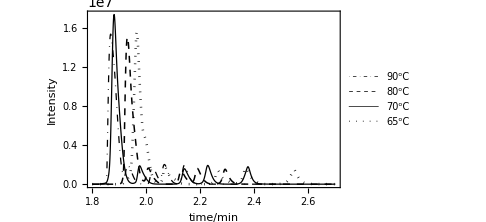

```mathematica
ListLinePlot[(Select[#,1.8<#[[1]]<2.7&]&/@A/@Table[i,{i,8,11}]),PlotRange->All,Frame->True,Axes->False,ImageSize->Medium,PlotStyle->{{DotDashed,Black,Thickness[0.0025]},{Dashed,Black,Thickness[0.003]},{Black,Thickness[0.0025]},{Dotted,Black,Thickness[0.005]}},PlotLegends->{"90^oC","80^oC","70^oC","65^oC"},FrameLabel->{"time/min","Intensity"}]
```

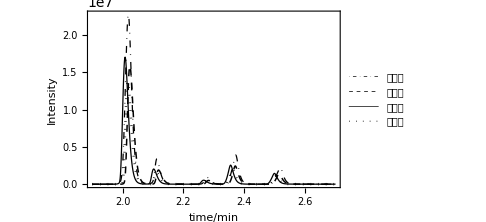

```mathematica
ListLinePlot[(Select[#,1.9<#[[1]]<2.7&]&/@A/@Table[i,{i,12,15}]),PlotRange->All,Frame->True,Axes->False,ImageSize->Medium,PlotStyle->{{DotDashed,Black,Thickness[0.0025]},{Dashed,Black,Thickness[0.003]},{Black,Thickness[0.0025]},{Dotted,Black,Thickness[0.005]}},PlotLegends->{"第一次","第二次","第三次","第四次"},FrameLabel->{"time/min","Intensity"}]
```

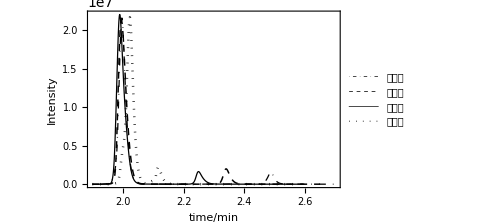

```mathematica
ListLinePlot[(Select[#,1.9<#[[1]]<2.7&]&/@A/@Table[i,{i,4,7}]),PlotRange->All,Frame->True,Axes->False,ImageSize->Medium,PlotStyle->{{DotDashed,Black,Thickness[0.0025]},{Dashed,Black,Thickness[0.003]},{Black,Thickness[0.0025]},{Dotted,Black,Thickness[0.005]}},PlotLegends->{"正丁醇","异丁醇","仲丁醇","叔丁醇"},FrameLabel->{"time/min","Intensity"}]
```

```mathematica
program[data_]:=Module[{PeakList,result={},operation},
operation[list_,peakinfo_]:=Module[{point,i=peakinfo[[1]],k=peakinfo[[1]]},
point=list[[peakinfo[[1]]]];
While[point[[2]]>peakinfo[[2]]/2,point=list[[++i]]];
point=list[[peakinfo[[1]]]];
While[point[[2]]>peakinfo[[2]]/2,point=list[[--k]]];
AppendTo[result,{list[[k]],list[[peakinfo[[1]]]],list[[i]]}]
];
PeakList=FindPeaks[Last/@data,0,0,100000];
operation[data,#]&/@PeakList;
result
]
(*该program为寻找气相色谱中大于100000的峰的峰位及半峰点的信息*)
```

```mathematica
(#[[3,1]]-#[[1,1]]&/@program[A[#]][[{3,4}]])&/@{8,9,10,11}
```

{{0.02667,0.02666},{0.026,0.02533},{0.026,0.02466},{0.02667,0.02733}}

```mathematica
FindPeaks[Last/@A[8],0,0,100000]
```

{{2802,15359367},{2897,1988969},{3036,1655778},{3101,2013407},{3213,1948913}}

```mathematica
program[A[8]][[{3,4}]]
```

{{{2.0145,794077},{2.02383,1655778},{2.04117,796354}},{{2.05717,977274},{2.06717,2013407},{2.08383,960182}}}

```mathematica
table1={{{2.083,2588767},{2.086,2503002},{2.086,2798238}},{{2.248,2228601},{2.251,2145371},{2.252,2457889}},{{2.334,2628089},{2.337,2524540},{2.338,2940840}},{{2.481,2510860},{2.484,2413107},{2.486,2852094}}};
table2={{{2.113,4383773},{2.119,2623718},{2.103,3693649},{2.112,2170869}},{{2.277,1306267},{2.283,740094},{2.267,767346},{2.276,591332}},{{2.372,6184906},{2.371,3457951},{2.355,3543378},{2.362,2661866}},{{2.518,3815628},{2.515,2086877},{2.5,2116732},{2.505,1527732}}};
```

```mathematica
Flatten/@table2//TableForm//TeXForm
```

\begin{array}{cccccccc}
 2.113 & 4383773 & 2.119 & 2623718 & 2.103 & 3693649 & 2.112 & 2170869 \\
 2.277 & 1306267 & 2.283 & 740094 & 2.267 & 767346 & 2.276 & 591332 \\
 2.372 & 6184906 & 2.371 & 3457951 & 2.355 & 3543378 & 2.362 & 2661866 \\
 2.518 & 3815628 & 2.515 & 2086877 & 2.5 & 2116732 & 2.505 & 1527732 \\
\end{array}

```mathematica
#[[2]]/@table1//TableForm
```

Part::partw: Part 2 of #1 does not exist.

#1⟦2⟧[{{2.083,2588767},{2.086,2503002},{2.086,2798238}}]
#1⟦2⟧[{{2.248,2228601},{2.251,2145371},{2.252,2457889}}]
#1⟦2⟧[{{2.334,2628089},{2.337,2524540},{2.338,2940840}}]
#1⟦2⟧[{{2.481,2510860},{2.484,2413107},{2.486,2852094}}]

```mathematica
#/Last[#]&[Last/@Total/@table1/3]//N
```

{1.01465,0.878576,1.04082,1.}